### MaTeX installation - execute only if MaTeX not installed

```mathematica
ResourceFunction["MaTeXInstall"][]
```

PacletObject[…]

### Loading MaTeX and its preamble for his notebook

```mathematica
<<MaTeX`
```

```mathematica
SetOptions[MaTeX,"Preamble"->{"\\usepackage{mathrsfs}\\DeclareSymbolFontAlphabet{\\mathrsfs}{rsfs}
\\newcommand{\\scri}{\\mathrsfs{I}}"}]
```

{BasePreamble→{\usepackage{lmodern,exscale},\usepackage{amsmath,amssymb}},Preamble→{\usepackage{mathrsfs}\DeclareSymbolFontAlphabet{\mathrsfs}{rsfs}
\newcommand{\scri}{\mathrsfs{I}}},DisplayStyle→True,ContentPadding→True,LineSpacing→{1.2,0},FontSize→12,Magnification→1,LogFileFunction→None,TeXFileFunction→None}

```mathematica
MaTeX["\\scri^+"]
```

-Graphics-

### Carter-Penrose diagram - flat space-time

#### Equations

```mathematica
uf = t[] - r[]; vf = t[] + r[];
```

```mathematica
Uf = ArcTan[uf]; Vf = ArcTan[vf];
```

```mathematica
Tf = Uf + Vf; Rf = Vf - Uf;
```

```mathematica
thf[Kcmc_] := {t[] -> t[] + Sqrt[aa^2 + r[]^2]} /. aa -> 3/Kcmc;
```

```mathematica
listrf[rval_] := {Rf, Tf} /. {r[] -> rval}
listtf[tval_] := {Rf, Tf} /. {t[] -> tval}
```

```mathematica
listuf[uval_] := {ArcTan[vvf] - ArcTan[uuf],    ArcTan[uuf] + ArcTan[vvf]} /. {uuf -> uval}
listvf[vval_] := {ArcTan[vvf] - ArcTan[uuf],    ArcTan[uuf] + ArcTan[vvf]} /. {vvf -> vval}
```

```mathematica
listttf[tval_, va_] := {Rf, Tf} /. thf[va] /. {t[] -> tval}
```

#### Initial

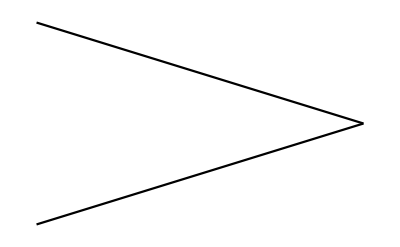
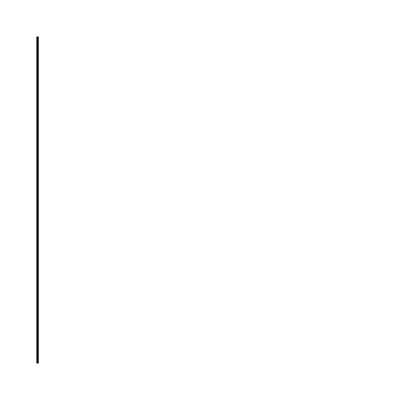

```mathematica
cover = {Plot[{x - π, π - x}, {x, 0, π}, 
   PlotRange -> {{0, π}, {-π, π}}, Ticks -> None, 
   PlotStyle -> Black, Axes -> None(*,AspectRatio->1*)], 
  ContourPlot[x == 0, {x, -0.01, π}, {y, -π, π}, Axes -> None, 
   Frame -> None, ContourStyle -> Black]}
```

```mathematica
labe = 22;
```

```mathematica
letters = Graphics[{Text["\!\(\*SuperscriptBox[\(i\), \(\(\\\ \)\(+\)\)]\)", {0 + 0.2, π +  0.4}, BaseStyle -> {FontSize -> labe,FontFamily->Times}],    Text["\!\(\*SuperscriptBox[\(i\), \(\(\\\ \)\(-\)\)]\)", {0 +  0.2, -π - 0.4}, BaseStyle -> {FontSize -> labe,FontFamily->Times}],    Text["\!\(\*SuperscriptBox[\(i\), \(\(\\\ \)\(0\)\)]\)", {π + 0.4, 0},  BaseStyle -> {FontSize -> labe,FontFamily->Times}],  Text[MaTeX["\\scri^+",Magnification->2], {π/2 + 0.3, π/2 + 0.3}], 
   Text[MaTeX["\\scri^-",Magnification->2], {π/2 + 0.3, -π/2 - 0.3}]},  PlotRange -> {{0 - 0.6, π + 0.6}, {-π - 0.6, π + 0.6}}]
```

-Graphics-

```mathematica
makePlotLegend[names_, markers_, origin_, markerSize_, fontSize_, font_] := 
  Join @@ Table[{Text[Style[names[[i]], FontSize -> fontSize, FontFamily->font], 
      Offset[{1.5*markerSize, -(i - 0.5)*Max[markerSize, fontSize]*1.25}, 
       Scaled[origin]], {-1, 0}], 
     Inset[Show[markers[[i]], ImageSize -> markerSize], 
      Offset[{markerSize/2, -(i - 0.5)*Max[markerSize, fontSize]*1.25}, 
       Scaled[origin]], {0, 0}, 
      Background -> Directive[Opacity[0], White]]}, {i, 1, 
     Length[names]}];(*copied from \
http://stackoverflow.com/questions/3463437/plotting-legends-in-mathematica*)
```

#### Graphs

```mathematica
listtime =   Map[listtf[#] &, {0, 0.3, 0.8, 1.6, 4, 15, -0.3, -0.8, -1.6, -4, -15}];
```

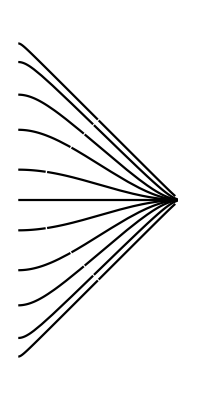

```mathematica
time = ParametricPlot[listtime, {r[], 0, 25},   PlotRange -> {{0, π}, {-π, π}}, Ticks -> None, Axes -> None,   PlotStyle ->{{Black}}]
```

```mathematica
listradius = Map[listrf[#] &, {0, 0.3, 0.8, 1.6, 4, 15}];
```

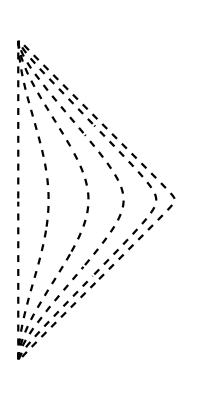

```mathematica
space = ParametricPlot[listradius, {t[], -25, 25},   PlotRange -> {{0, π}, {-π, π}}, Ticks -> None, Axes -> None,   PlotStyle ->(* Green*){{Black,Dashed}}]
```

```mathematica
(*Show[time,space,cover,letters,PlotRange->{{0-0.4,π+0.7},{-π-0.6,π+0.6}},Epilog->makePlotLegend[{"t = const","r = const"},(Graphics[{#,Line[{{-1,0},{1,0}}]}])&/@{Red,Green},{0.48,0.18},labe-2,labe-2,"Arial"]]*)Show[time,space,cover,letters,PlotRange->{{0,π+0.6},{-π-0.6,π+0.6}},Epilog->makePlotLegend[{"r = const","t = const"},(Graphics[{#,Line[{{-1,0},{1,0}}]}])&/@{Dashed,Black},{0.46,0.18},labe-2,labe-2,"Times"],ImageSize->{260,450}]
```

-Graphics-

```mathematica
(*example of old diagrams*)
```

```mathematica
listlightout=Map[listuf[#]&,{-2.5,-1.1,-0.5,-0.1,0.3,0.8,1.6,4}];
listlightin=Map[listvf[#]&,{-2.5,-1.1,-0.5,-0.1,0.3,0.8,1.6,4}];
```

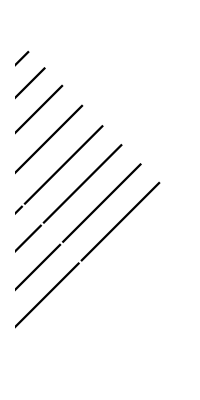

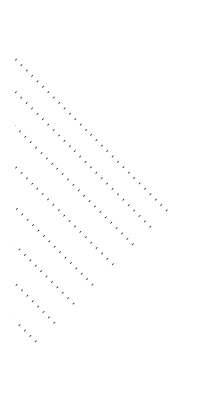

```mathematica
lightout=ParametricPlot[listlightout,{vvf,-25,25},PlotRange->{{0,π},{-π,π}},Ticks->None,Axes->None,PlotStyle->(*Blue*)Black]
lightin=ParametricPlot[listlightin,{uuf,-25,25},PlotRange->{{0,π},{-π,π}},Ticks->None,Axes->None,PlotStyle->{{Black,Dotted}}]
```

```mathematica
Show[space,lightout,(*lightin,*)cover,letters,PlotRange->{{0,π+0.6},{-π-0.6,π+0.6}},Epilog->makePlotLegend[{"r = const","light ray"},(Graphics[{#,Line[{{-1,0},{1,0}}]}])&/@{Dashed,Black},{0.46,0.18},labe-2,labe-2,"Times"],ImageSize->{260,450}]
```

-Graphics-

```mathematica
timecut = ParametricPlot[listtime, {r[], 0, 1.6},   PlotRange -> {{0, π}, {-π, π}}, Ticks -> None, Axes -> None,   PlotStyle ->(* Red*)Black];
timecutout = ParametricPlot[listtime, {r[], 1.6, 100},   PlotRange -> {{0, π}, {-π, π}}, Ticks -> None, Axes -> None,   PlotStyle ->(* Red*){{Gray}}];
cutradius=ParametricPlot[listrf[1.6], {t[], -100, 100},   PlotRange -> {{0, π}, {-π, π}}, Ticks -> None, Axes -> None,   PlotStyle ->(* Green*){{Black,Thick,Dashed}}];
spacecut= ParametricPlot[Map[listrf[#] &, {0, 0.3, 0.8,  4, 15}], {t[], -100, 100},   PlotRange -> {{0, π}, {-π, π}}, Ticks -> None, Axes -> None,   PlotStyle ->(* Green*){{Black,Dashed}}];
```

```mathematica
Show[cutradius,timecut,timecutout,spacecut,cover,letters,PlotRange->{{0,π+0.6},{-π-0.6,π+0.6}},Epilog->makePlotLegend[{"r = const","t = const"},(Graphics[{#,Line[{{-1,0},{1,0}}]}])&/@{Dashed,Black},{0.46,0.18},labe-2,labe-2,"Times"],ImageSize->{260,450}]
```

-Graphics-

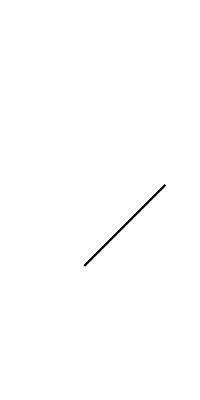
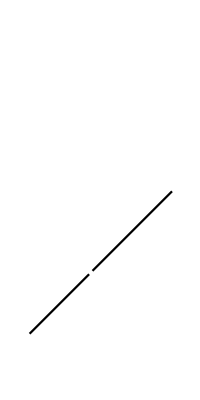
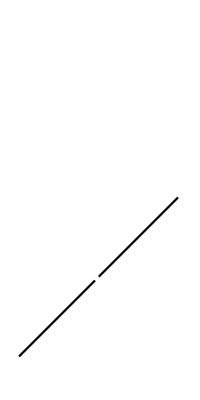
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*Map[listtf[#] &, {0, 0.3, 0.8, 1.6, 4, 15, -0.3, -0.8, -1.6, -4, -15}];*)
lightcut={ParametricPlot[{listuf[-1.6]},{vvf,1.6,100},PlotRange->{{0,π},{-π,π}},Ticks->None,Axes->None,PlotStyle->(*Blue*)Black],ParametricPlot[{listuf[-1.3]},{vvf,1.9,100},PlotRange->{{0,π},{-π,π}},Ticks->None,Axes->None,PlotStyle->(*Blue*)Black],ParametricPlot[{listuf[-0.8]},{vvf,2.4,100},PlotRange->{{0,π},{-π,π}},Ticks->None,Axes->None,PlotStyle->(*Blue*)Black],ParametricPlot[{listuf[0]},{vvf,3.2,100},PlotRange->{{0,π},{-π,π}},Ticks->None,Axes->None,PlotStyle->(*Blue*)Black],ParametricPlot[{listuf[2.4]},{vvf,5.6,100},PlotRange->{{0,π},{-π,π}},Ticks->None,Axes->None,PlotStyle->(*Blue*)Black],ParametricPlot[{listuf[13.4]},{vvf,16.6,100},PlotRange->{{0,π},{-π,π}},Ticks->None,Axes->None,PlotStyle->(*Blue*)Black],ParametricPlot[{listuf[-1.9]},{vvf,1.3,100},PlotRange->{{0,π},{-π,π}},Ticks->None,Axes->None,PlotStyle->(*Blue*)Black],ParametricPlot[{listuf[-2.4]},{vvf,0.8,100},PlotRange->{{0,π},{-π,π}},Ticks->None,Axes->None,PlotStyle->(*Blue*)Black],ParametricPlot[{listuf[-3.2]},{vvf,0,100},PlotRange->{{0,π},{-π,π}},Ticks->None,Axes->None,PlotStyle->(*Blue*)Black],ParametricPlot[{listuf[-5.6]},{vvf,-2.4,100},PlotRange->{{0,π},{-π,π}},Ticks->None,Axes->None,PlotStyle->(*Blue*)Black],ParametricPlot[{listuf[-16.6]},{vvf,-13.4,100},PlotRange->{{0,π},{-π,π}},Ticks->None,Axes->None,PlotStyle->(*Blue*)Black]}
```

```mathematica
Show[lightcut,timecut,cutradius,space,cover,letters,PlotRange->{{0,π+0.6},{-π-0.6,π+0.6}},Epilog->makePlotLegend[{"r = const","matched"},(Graphics[{#,Line[{{-1,0},{1,0}}]}])&/@{Dashed,Black},{0.46,0.18},labe-2,labe-2,"Arial"],ImageSize->{260,450}]
```

-Graphics-

```mathematica
listradiush=Map[listrf[#]&,{0,0.2,0.5,1,2,5,10}];
```

```mathematica
spaceh=ParametricPlot[listradius,{t[],-25,25},PlotRange->{{0,π},{-π,π}},Ticks->None,Axes->None,PlotStyle->{{(*Green*)Black,Dashed}},BaseStyle->{FontSize->labe-2(*16*)}(*,PlotLabel->"a = "<>ToString[aa]*)]
```

-Graphics-

```mathematica
Kcmcset=6;
```

```mathematica
hlist[va_]:=Map[listttf[#,va]&,{0,0.2,0.5,1,2,5,10,-0.2,-0.5,-1,-2,-5,-10}]
```

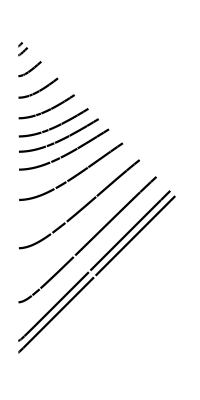

```mathematica
phl=ParametricPlot[hlist[Kcmcset],{r[],0,25},PlotRange->{{0,π},{-π,π}},Ticks->None,PlotStyle->(*Red*)Black,BaseStyle->{FontSize->labe-2(*16*)}(*,PlotLabel->"a = "<>ToString[aa]*),Axes->None]
```

```mathematica
Kfval=Graphics[{Text["|K_CMC| = "<>ToString[Kcmcset],{π/2+0.9,π/2+1.5},BaseStyle->{FontFamily->"Times",FontSize->labe+2}]},PlotRange->{{0-0.6,π+0.6},{-π-0.6,π+0.6}}]
```

-Graphics-

```mathematica
Show[spaceh,phl,Kfval,cover,letters,PlotRange->{{0,π+0.6},{-π-0.6,π+0.6}},Epilog->makePlotLegend[{"r = const","t = const"},(Graphics[{#,Line[{{-1,0},{1,0}}]}])&/@{Dashed,Black},{0.46,0.18},labe-2,labe-2,"Times"],ImageSize->{260,450}]
```

-Graphics-